```mathematica
AppendTo[$Path,FileNameJoin[{$HomeDirectory,"GDC","DialecticalStructures"}]];
If[!MemberQ[$Path,FileNameJoin[{$HomeDirectory,"GDC","DialecticalStructures"}]],AppendTo[$Path,FileNameJoin[{$HomeDirectory,"GDC","DialecticalStructures"}]]];
Print["Package path ",FindFile["GDCAnalysis3`"]];
Print["Package path ",FindFile["GDCComparisons`"]];
<<GDCComparisons`
<<GDCAnalysis3`
```

Package path /home/carla/GDC/DialecticalStructures/GDCAnalysis3.m

Package path /home/carla/GDC/DialecticalStructures/GDCComparisons.m

```mathematica
acc=Get["/home/carla/GDC/Comparisons/Veritism/ACC/gdc_ACC_EVBK.txt"]
doj=FileNames["/home/carla/GDC/CH_Pool/*/gdc_DOJ_VV_CHMAX_*.txt"];
z=FileNames["/home/carla/GDC/CH_Pool/*/gdc_Z_VV_CHMAX_*.txt"];
f=FileNames["/home/carla/GDC/CH_Pool/*/gdc_F_VV_CHMAX_*.txt"];
names=Map[StringTake[#,{-7,-5}]&,doj]
```

<|DLB→{{0,0.866667},{0.5,0.875},{1,0.909091},{1.5,0.928571},{2,0.954545},{2.5,0.958333},{3,1.},{3.5,1.},{4,0.969697},{4.5,0.970588},{5,0.944444},{5.5,0.944444},{6,0.923077},{6.5,0.925},{7,0.880952},{7.5,0.888889},{8,1.}},MUR→{{1,0.9},{1.5,0.923077},{2,0.916667},{2.5,0.923077},{3,0.933333},{3.5,0.941176},{4,0.891892},{4.5,0.894737},{5,0.902439},{5.5,0.902439},{6,0.837209},{6.5,0.840909},{7,0.97619},{7.5,0.977778},{8,1.}},LYE→{{1,0.894737},{1.5,0.92},{2,0.909091},{2.5,0.916667},{3,0.923077},{3.5,0.933333},{4,0.90625},{4.5,0.909091},{5,0.857143},{5.5,0.857143},{6,0.861111},{6.5,0.864865},{7,0.926829},{7.5,0.931818},{8,1.}},PHI→{{2,1.},{2.5,1.},{3,1.},{3.5,1.},{4,1.},{4.5,1.},{5,0.971429},{5.5,0.971429},{6,0.944444},{6.5,0.945946},{7,0.925},{7.5,0.930233},{8,1.}},SED→{{3,1.},{3.5,1.},{4,0.911765},{4.5,0.914286},{5,0.894737},{5.5,0.894737},{6,0.871795},{6.5,0.875},{7,0.863636},{7.5,0.87234},{8,1.}},AUS→{{6,0.975},{6.5,0.97561},{7,0.954545},{7.5,0.957447},{8,1.}}|>

{AUS,DLB,LYE,MUR,PHI,SED}

```mathematica
dojVVCHMax=<|Map[StringTake[#,{-7,-5}]->Get[#]&,doj]|>;
zVVCHMax=<|Map[StringTake[#,{-7,-5}]->Get[#]&,z]|>;
fVVCHMax=<|Map[StringTake[#,{-7,-5}]->Get[#]&,f]|>;
```

```mathematica
dojVVCHMax[["DLB"]][[1;;3]]
acc[["DLB"]][[1;;3]]
```

{{0,0.6},{0.5,0.6},{1,0.6}}

{{0,0.866667},{0.5,0.875},{1,0.909091}}

```mathematica
(*dojVVCHMax[["AUS"]]
acc[["AUS"]]
pointsDOJ=Flatten[Map[pointsWithoutPersons[acc, dojVVCHMax, #]&,{"AUS"}],2]*)
pointsDOJ=Flatten[Map[pointsWithoutPersons[acc, dojVVCHMax, #]&,names],2];
pointsZ=Flatten[Map[pointsWithoutPersons[acc, zVVCHMax, #]&,names],2];
pointsF=Flatten[Map[pointsWithoutPersons[acc, fVVCHMax, #]&,names],2];
minPoint=Min@Union[pointsDOJ[[All,1]],pointsZ[[All,1]],pointsF[[All,1]]]
```

0.837209

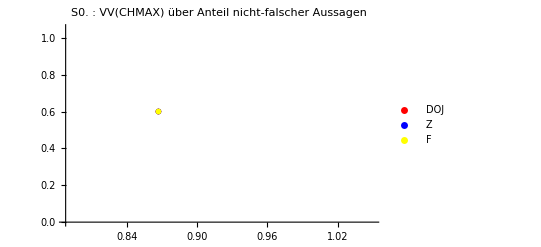
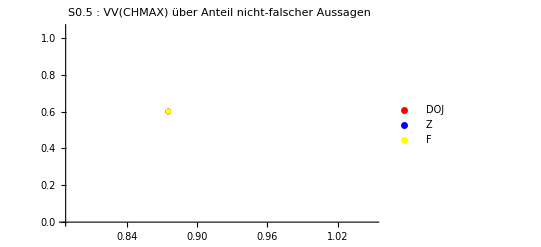
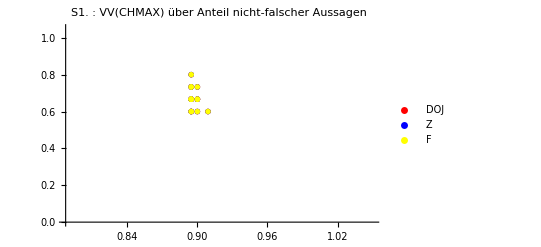
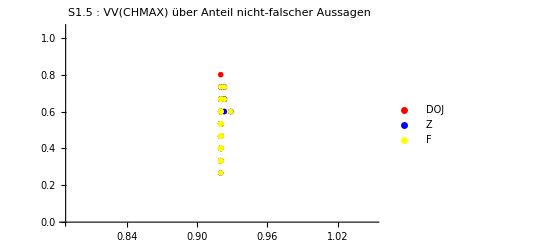
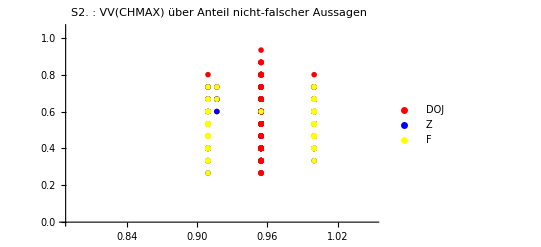
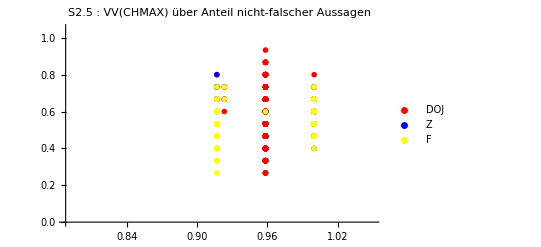
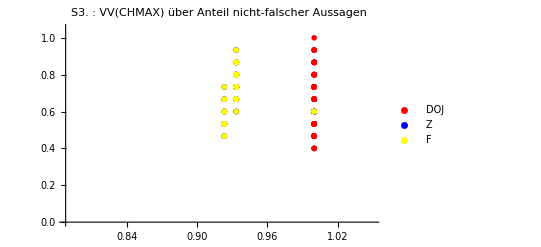
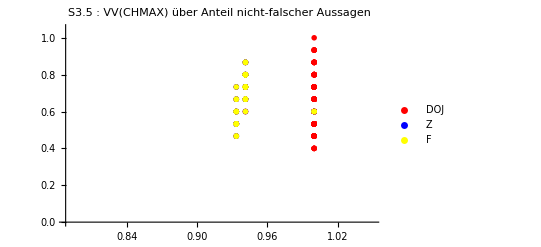
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- |

```mathematica
(*ListPlot[{pointsDOJ,pointsZ,pointsF}, PlotLegends->{"DOJ","Z","F"},PlotStyle->{Red,Blue,Yellow},ImageSize->400, 
PlotRange->{{minPoint-0.05,1.05},{0,1.05}},PlotMarkers->{{"D",12},{"Z",12},{"F",12}},
PlotLabel->"VV(CHMAX) über Anteil nicht-falscher Aussagen"]*)
pointsPerTimeStep=Map[Function[z,
Map[Function[y,Flatten[Map[Function[x,pointsSXWP[acc,y,x,(z-1)*0.5]],names],1]],{dojVVCHMax,zVVCHMax,fVVCHMax}]],Range[17]];

plotsSX=Map[ListPlot[pointsPerTimeStep[[#]], PlotLegends->{"DOJ","Z","F"},PlotStyle->{Red,Blue,Yellow},ImageSize->400,PlotRange->{{minPoint-0.05,1.05},{0,1.05}},PlotMarkers->{{"D",12},{"Z",12},{"F",12}},PlotLabel->"S"<>ToString[(#-1)*0.5]<>" : VV(CHMAX) über Anteil nicht-falscher Aussagen"]&,Range[17]];
plotsSXOut=Grid[{plotsSX[[1;;3]],plotsSX[[4;;6]],plotsSX[[7;;9]],plotsSX[[10;;12]],plotsSX[[13;;15]],plotsSX[[16;;17]]},ItemSize->35]
```

```mathematica
SetDirectory["/home/carla/GDC/Comparisons/Veritism/BRIDGE/"];
Export["VV_CHMAX_Anteil_nicht_falscher_Aussagen.jpeg",plotsSXOut,ImageResolution->300]
```

VV_CHMAX_Anteil_nicht_falscher_Aussagen.jpeg

```mathematica
pointsPerTimeStep[[1]]
Length@pointsPerTimeStep[[1]]
```

{{{0.866667,0.6}},{{0.866667,0.6}},{{0.866667,0.6}}}

3

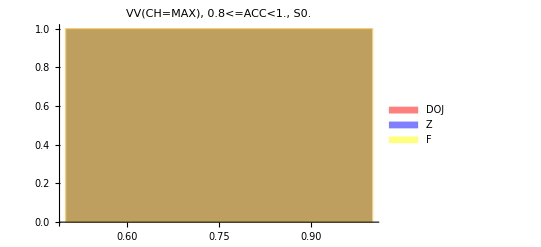
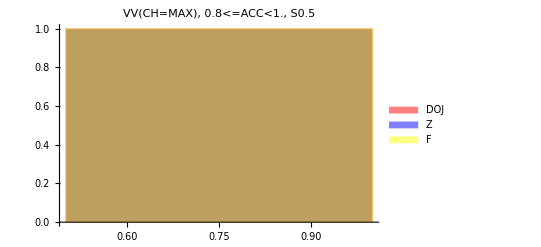
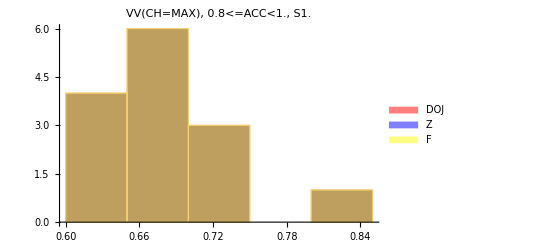
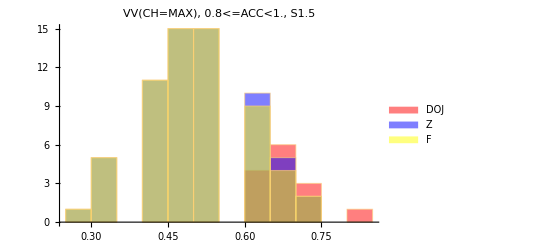
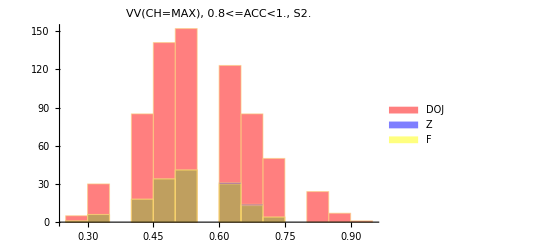
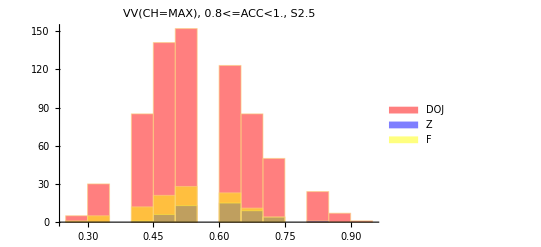
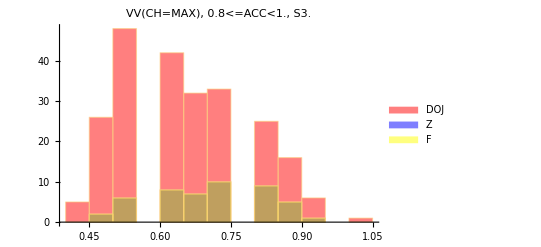
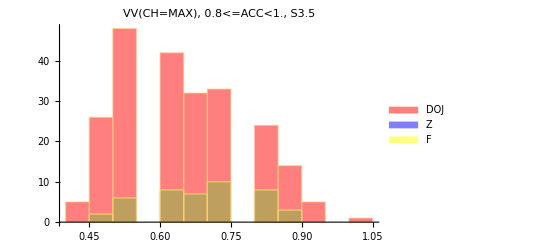
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- |

```mathematica
histSXACC0810=Map[histoAccFunc[pointsPerTimeStep[[#]],0.8,1.0,ToString[(#-1)*0.5]]&, Range[17]];
histSXACC0810Out=Grid[{histSXACC0810[[1;;3]],histSXACC0810[[4;;6]],histSXACC0810[[7;;9]],histSXACC0810[[10;;12]],
histSXACC0810[[13;;15]],histSXACC0810[[16;;17]]},ItemSize->35]
```

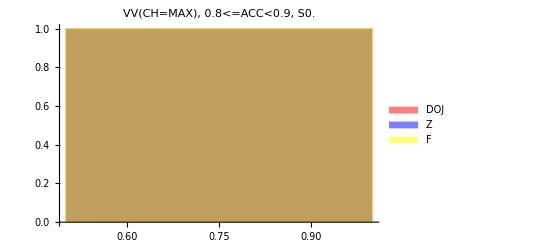
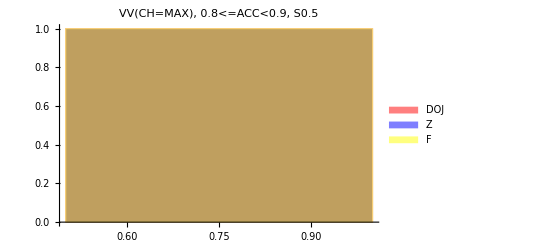
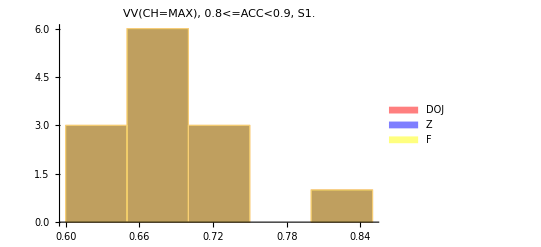
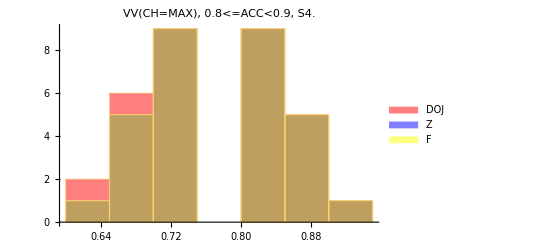
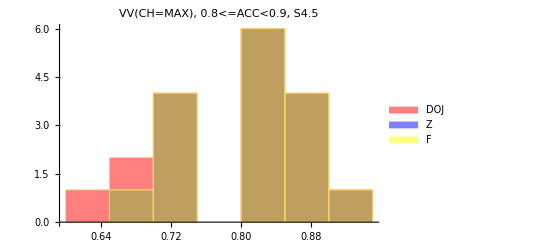
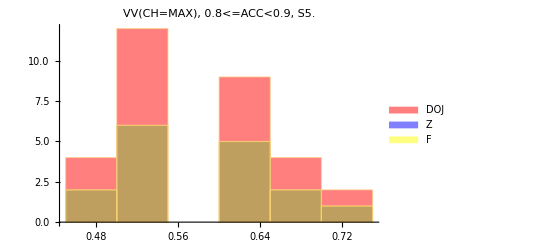
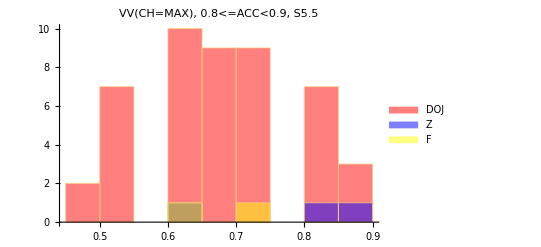
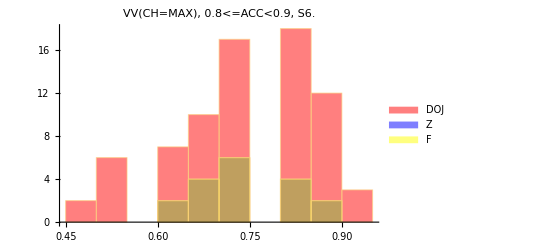
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- |

```mathematica
histSXACC0809=Map[histoAccFunc[pointsPerTimeStep[[#]],0.8,0.9,ToString[(#-1)*0.5]]&, Range[17]];
histSXACC0809Out=Grid[{histSXACC0809[[1;;3]],histSXACC0809[[4;;6]],histSXACC0809[[7;;9]],histSXACC0809[[10;;12]],
histSXACC0809[[13;;15]],histSXACC0809[[16;;17]]},ItemSize->35]
```

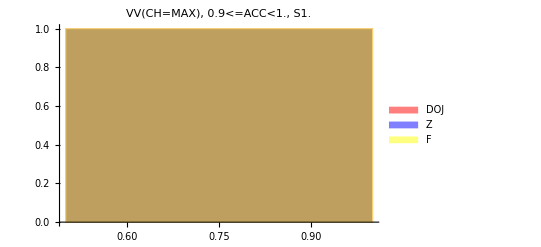
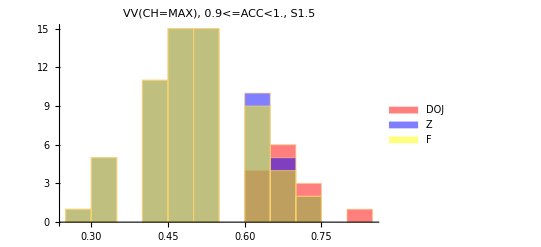
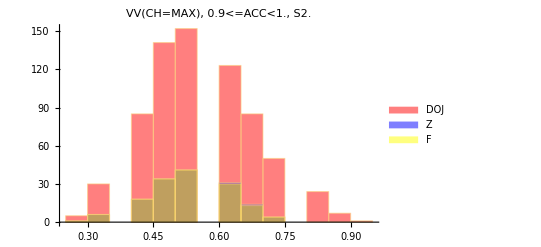
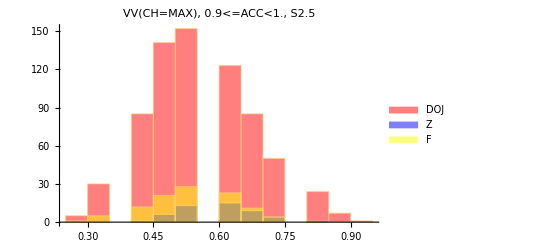
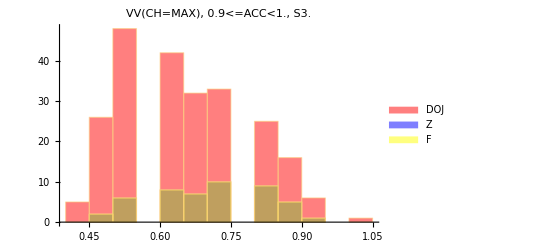
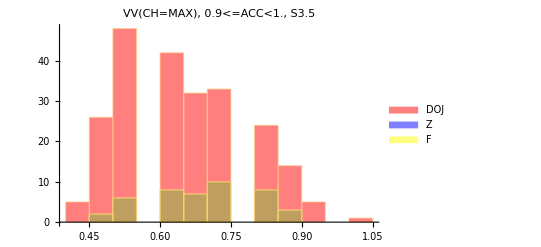
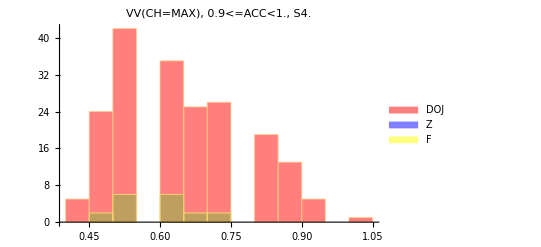
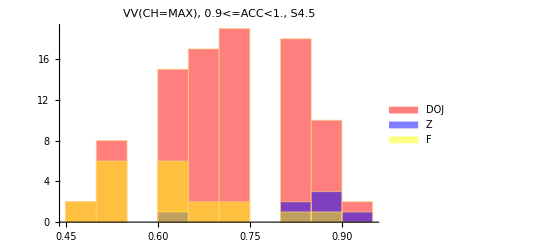
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- |

```mathematica
histSXACC0910=Map[histoAccFunc[pointsPerTimeStep[[#]],0.9,1.0,ToString[(#-1)*0.5]]&, Range[17]];
histSXACC0910Out=Grid[{histSXACC0910[[1;;3]],histSXACC0910[[4;;6]],histSXACC0910[[7;;9]],histSXACC0910[[10;;12]],
histSXACC0910[[13;;15]],histSXACC0910[[16;;17]]},ItemSize->35]
```

```mathematica
SetDirectory["/home/carla/GDC/Comparisons/Veritism/BRIDGE/"];
Export["HIST_VV_ACC_0_8_1_0.jpeg",histSXACC0810Out,ImageResolution->300]
Export["HIST_VV_ACC_0_8_0_9.jpeg",histSXACC0809Out,ImageResolution->300]
Export["HIST_VV_ACC_0_9_1_0.jpeg",histSXACC0910Out,ImageResolution->300]
```

HIST_VV_ACC_0_8_1_0.jpeg

HIST_VV_ACC_0_8_0_9.jpeg

HIST_VV_ACC_0_9_1_0.jpeg

```mathematica
Sort@Counts@Cases[pointsDOJ,p_/;p[[1]]==0.9583333333333334]
(*histSXACC085=Map[histoAccFunc[pointsPerTimeStep[[#]],0.8571428571428572,"NULL",ToString[#-1]]&, Range[9]];
histSXACC085Out=Grid[{histSXACC085[[1;;3]],histSXACC085[[4;;6]],histSXACC085[[7;;9]]},ItemSize->35]*)
```

<|{0.958333,0.933333}→1,{0.958333,0.266667}→5,{0.958333,0.866667}→7,{0.958333,0.8}→22,{0.958333,0.333333}→30,{0.958333,0.733333}→45,{0.958333,0.666667}→75,{0.958333,0.4}→85,{0.958333,0.6}→118,{0.958333,0.466667}→141,{0.958333,0.533333}→152|>

```mathematica
(*DOJ-Häufung bei Anteil nicht-falscher Aussagen von 0.857143 HAT SICH JETZT NACH OBEN VERSCHOBEN!!!
Das entspricht einem Verhältnis von 1:7 zwischen falschen Aussagen in und Gesamtanzahl von EVBK=PERS 
|EVBK|=7 (4x), 14 (3x) oder 21 (3x)  von insgesamt 41 *)
N[1-(1/7)]
posList=Map[Get[#]&,FileNames["/home/carla/GDC/POS/*.txt"]];
ts={0,1,2,3,4,5,6,7,8};
numEVBK=<|"DLB"->numEVBKFunc[posList, "DLB",ts+1],"MUR"->numEVBKFunc[posList, "MUR",Drop[ts+1,1]],
"LYE"->numEVBKFunc[posList, "LYE",Drop[ts+1,1]], "PHI"->numEVBKFunc[posList, "PHI",Drop[ts+1,2]],
"SED"->numEVBKFunc[posList, "SED",Drop[ts+1,3]],"AUS"->numEVBKFunc[posList, "AUS",Drop[ts+1,6]]|>
Sort@Counts@Flatten[Values[numEVBK][[All,2]],1]
Length[Flatten[Values[numEVBK][[All,2]],1]]
```

0.857143

Part::pspec1: Part specification DLB is not applicable.

Part::pspec1: Part specification BK is not applicable.

Part::pspec1: Part specification DLB is not applicable.

General::stop: Further output of Part::pspec1 will be suppressed during this calculation.

Part::pkspec1: The expression {<|name→CON,CH→{},BK→{Standard Sequence,Formation of strata,Main Culm as Post-Primary and Pre-NRS,BCL as Post-Primary and Pre-NRS,Non-Culm as Post-Primary and Pre-NRS,BCL Older Than MC,Conformable Passage - MC and BCL},EV→{CM Plants in Devon Culm}|>,«4»,<|name→USS,CH→{Unbroken Sequence of Devon Strata},BK→{},EV→{}|>}⟦DLB⟧ cannot be used as a part specification.

Part::pkspec1: The expression {<|name→CON,CH→{},BK→{Standard Sequence,Formation of strata,Main Culm as Post-Primary and Pre-NRS,BCL as Post-Primary and Pre-NRS,Non-Culm as Post-Primary and Pre-NRS,BCL Older Than MC,Conformable Passage - MC and BCL},EV→{Scottish ORS - Rocks,CM Plants in Devon Culm}|>,«8»,<|name→LP1,CH→{Lyellian Principle},BK→{},EV→{}|>}⟦DLB⟧ cannot be used as a part specification.

Part::pkspec1: The expression {<|name→CON,CH→{},BK→{Standard Sequence,Formation of strata,Main Culm as Post-Primary and Pre-NRS,BCL as Post-Primary and Pre-NRS,Non-Culm as Post-Primary and Pre-NRS,BCL Older Than MC,Conformable Passage - MC and BCL,Characteristic Rock Type,Characteristic Fossil,Characteristic Fossil Assemblage,Pembrokeshire - CM in Age},EV→{LV in Fauna and Flora -Today,Pembrokeshire - Appearance,Scottish ORS - Rocks,CM Plants in Devon Culm}|>,«12»,<|name→AP1,CH→{Characteristic Fossil Assemblage Principle},BK→{},EV→{}|>}⟦DLB⟧ cannot be used as a part specification.

General::stop: Further output of Part::pkspec1 will be suppressed during this calculation.

<|DLB→{3.,{3,3,3,3,3,3,3,3,3}},MUR→{3.,{3,3,3,3,3,3,3,3}},LYE→{3.,{3,3,3,3,3,3,3,3}},PHI→{3.,{3,3,3,3,3,3,3}},SED→{3.,{3,3,3,3,3,3}},AUS→{3.,{3,3,3}}|>

<|3→41|>

41

```mathematica
(*VV(CH-MAX)=0.8 bedeutet, dass 12 atomare Datierungen von insgesamt 15 übereinstimmen, 
z.Bsp MC=CM+ML,BCL=ML+ORS,NC=ORS+SIL
Für die Klasse der Datierungen, die jeder Schicht lediglich ein Alter zuordnet gilt: Mind.9 Übereinstimmungen, VV≥0.6 *)
{Min@pointsDOJ[[All,2]],Min@pointsZ[[All,2]],Min@pointsF[[All,2]]}
{4/15.,9/15.,12/15.,13/15.,14/15.}
```

{0.266667,0.266667,0.266667}

{0.266667,0.6,0.8,0.866667,0.933333}

```mathematica
(*Häufigkeit einer POS mit lediglich 4 Übereinstimmungen*)
{Length@Cases[pointsDOJ[[All,2]], p_/; p==N[4/15]],Length@Cases[pointsZ[[All,2]], p_/; p==N[4/15]],Length@Cases[pointsF[[All,2]], p_/; p==N[4/15]]}
(*Häufigkeit einer POS mit lediglich 6 Übereinstimmungen, Bsp. ML+ORS/ORS+SIL/SIL+CAM*)
{Length@Cases[pointsDOJ[[All,2]], p_/; p==N[6/15]],Length@Cases[pointsZ[[All,2]], p_/; p==N[6/15]],Length@Cases[pointsF[[All,2]], p_/; p==N[6/15]]}
(*Häufigkeit einer POS mit 10 Übereinstimmungen, Bsp. SIL/SIL+CAM/CAM*)
{Length@Cases[pointsDOJ[[All,2]], p_/; p==N[8/15]],Length@Cases[pointsZ[[All,2]], p_/; p==N[8/15]],Length@Cases[pointsF[[All,2]], p_/; p==N[8/15]]}
(*Häufigkeit einer POS mit 9 Übereinstimmungen, Bsp. CAM/CAM/CAM*)
{Length@Cases[pointsDOJ[[All,2]], p_/; p==N[9/15]],Length@Cases[pointsZ[[All,2]], p_/; p==N[9/15]],Length@Cases[pointsF[[All,2]], p_/; p==N[9/15]]}
(*Häufigkeit einer POS mit 10 Übereinstimmungen, Bsp. CM/CM/SIL+CAM*)
{Length@Cases[pointsDOJ[[All,2]], p_/; p==N[10/15]],Length@Cases[pointsZ[[All,2]], p_/; p==N[10/15]],Length@Cases[pointsF[[All,2]], p_/; p==N[10/15]]}
(*Häufigkeit einer POS mit 12 Übereinstimmungen, Bsp. CM/CM/ORS+SIL oder CM/ML/SIL+CAM*)
{Length@Cases[pointsDOJ[[All,2]], p_/; p==N[12/15]],Length@Cases[pointsZ[[All,2]], p_/; p==N[12/15]],Length@Cases[pointsF[[All,2]], p_/; p==N[12/15]]}
(*Häufigkeit einer POS totaler Übereinstimmung*)
{Length@Cases[pointsDOJ[[All,2]], p_/; p==1],Length@Cases[pointsZ[[All,2]], p_/; p==1],Length@Cases[pointsF[[All,2]], p_/; p==1]}
```

{10,2,3}

{205,30,41}

{631,93,114}

{596,108,115}

{469,74,76}

{330,49,46}

{19,7,9}

```mathematica
(*Filtern nach DENSITY bzw. SX

histoAccFunc[pointsDOJ, 0.6,1.0,"DOJ"]
histoAccFunc[pointsZ, 0.6,1.0,"Z"]
histoAccFunc[pointsF, 0.6,1.0,"F"]*)
```